## the chiral model

```mathematica
hx[J_,m_,eta_,kmag_,phik_]:=kmag^J Cos[J phik]
```

```mathematica
hy[J_,m_,eta_,kmag_,phik_]:=eta kmag^J Sin[J phik]
```

```mathematica
hz[J_,m_,eta_,kmag_,phik_]:=m
```

```mathematica
eplus[J_,m_,eta_,kmag_,phik_]:=(m^2+kmag^(2J))^(1/2)
```

```mathematica
Clear[J,m,eta,kmag,phik]
```

```mathematica
Simplify[(hx[J,m,eta,kmag,phik]+I hy[J,m,eta,kmag,phik])/Sqrt[hx[J,m,eta,kmag,phik]^2+hy[J,m,eta,kmag,phik]^2+(eplus[J,m,eta,kmag,phik]-m)^2]]
```

(kmag^J (Cos[J phik]+ⅈ eta Sin[J phik]))/(√((m-√(kmag^(2 J)+m^2))^2+kmag^(2 J) Cos[J phik]^2+eta^2 kmag^(2 J) Sin[J phik]^2))

```mathematica
Simplify[(eplus[J,m,eta,kmag,phik]-m)/Sqrt[hx[J,m,eta,kmag,phik]^2+hy[J,m,eta,kmag,phik]^2+(eplus[J,m,eta,kmag,phik]-m)^2]]
```

(-m+√(kmag^(2 J)+m^2))/(√((m-√(kmag^(2 J)+m^2))^2+kmag^(2 J) Cos[J phik]^2+eta^2 kmag^(2 J) Sin[J phik]^2))

```mathematica
uplus1[J_,m_,eta_,kmag_,phik_]:=(kmag^J (Cos[J phik]+ⅈ eta Sin[J phik]))/(√((m-√(kmag^(2 J)+m^2))^2+kmag^(2 J) Cos[J phik]^2+eta^2 kmag^(2 J) Sin[J phik]^2))
```

```mathematica
uplus2[J_,m_,eta_,kmag_,phik_]:=(-m+√(kmag^(2 J)+m^2))/(√((m-√(kmag^(2 J)+m^2))^2+kmag^(2 J) Cos[J phik]^2+eta^2 kmag^(2 J) Sin[J phik]^2))
```

```mathematica
uplus1conj[J_,m_,eta_,kmag_,phik_]:=(kmag^J (Cos[J phik]-ⅈ eta Sin[J phik]))/(√((m-√(kmag^(2 J)+m^2))^2+kmag^(2 J) Cos[J phik]^2+eta^2 kmag^(2 J) Sin[J phik]^2))
```

```mathematica
uplus2conj[J_,m_,eta_,kmag_,phik_]:=(-m+√(kmag^(2 J)+m^2))/(√((m-√(kmag^(2 J)+m^2))^2+kmag^(2 J) Cos[J phik]^2+eta^2 kmag^(2 J) Sin[J phik]^2))
```

```mathematica
Simplify[I(D[uplus1conj[J,m,eta,kmag,phik],kmag]D[uplus1[J,m,eta,kmag,phik],phik]+D[uplus2conj[J,m,eta,kmag,phik],kmag]D[uplus2[J,m,eta,kmag,phik],phik])-I(D[uplus1conj[J,m,eta,kmag,phik],phik]D[uplus1[J,m,eta,kmag,phik],kmag]+D[uplus2conj[J,m,eta,kmag,phik],phik]D[uplus2[J,m,eta,kmag,phik],kmag])]
```

(2 eta J^2 kmag^(-1+2 J) m (kmag^(2 J)+2 m (m-√(kmag^(2 J)+m^2))))/(√(kmag^(2 J)+m^2) (kmag^(2 J)+2 m^2-2 m √(kmag^(2 J)+m^2)+kmag^(2 J) Cos[J phik]^2+eta^2 kmag^(2 J) Sin[J phik]^2)^2)

```mathematica
berrycurv[J_,m_,eta_,kmag_,phik_]:=(2 eta J^2 kmag^(-1+2 J) m (kmag^(2 J)+2 m (m-√(kmag^(2 J)+m^2))))/(√(kmag^(2 J)+m^2) (kmag^(2 J)+2 m^2-2 m √(kmag^(2 J)+m^2)+kmag^(2 J) Cos[J phik]^2+eta^2 kmag^(2 J) Sin[J phik]^2)^2)
```

```mathematica
J=1;
m=0.1;
eta=1;
NIntegrate[berrycurv[J,m,eta,kmag,phik],{kmag,0.001,100},{phik,0,2π}]
```

3.13829

```mathematica
J=1;
m=1;
eta=1;
NIntegrate[berrycurv[J,m,eta,kmag,phik],{kmag,0.001,100},{phik,0,2π}]
```

3.11018

```mathematica
J=2;
m=0.1;
eta=1;
NIntegrate[berrycurv[J,m,eta,kmag,phik],{kmag,0.001,100},{phik,0,2π}]
```

6.28311

```mathematica
J=2;
m=1;
eta=1;
NIntegrate[berrycurv[J,m,eta,kmag,phik],{kmag,0.001,100},{phik,0,2π}]
```

6.28391

```mathematica
J=3;
m=0.1;
eta=1;
NIntegrate[berrycurv[J,m,eta,kmag,phik],{kmag,0.01,100},{phik,0,2π}]
```

9.42476

## lieb lattice

```mathematica
akfull[delta_,kx_,ky_]:=Cos[kx/2]+I delta Sin[kx/2]
```

```mathematica
bkfull[delta_,kx_,ky_]:=Cos[ky/2]+I delta Sin[ky/2]
```

```mathematica
akfullconj[delta_,kx_,ky_]:=Cos[kx/2]-I delta Sin[kx/2]
```

```mathematica
bkfullconj[delta_,kx_,ky_]:=Cos[ky/2]-I delta Sin[ky/2]
```

```mathematica
Clear[delta]
```

```mathematica
Simplify[Sqrt[akfull[delta,kx,ky]akfullconj[delta,kx,ky]+bkfull[delta,kx,ky]bkfullconj[delta,kx,ky]]]
```

(√(2+2 delta^2+Cos[kx]-delta^2 Cos[kx]+Cos[ky]-delta^2 Cos[ky]))/(√2)

```mathematica
eliebfull[delta_,kx_,ky_]:=(√(2+2 delta^2+Cos[kx]-delta^2 Cos[kx]+Cos[ky]-delta^2 Cos[ky]))/(√2)
```

```mathematica
(*middle band*)
```

```mathematica
umiddle1full[delta_,kx_,ky_]:=-bkfull[delta,kx,ky]/eliebfull[delta,kx,ky]
```

```mathematica
umiddle1fullconj[delta_,kx_,ky_]:=-bkfullconj[delta,kx,ky]/eliebfull[delta,kx,ky]
```

```mathematica
umiddle3full[delta_,kx_,ky_]:=akfullconj[delta,kx,ky]/eliebfull[delta,kx,ky]
```

```mathematica
umiddle3fullconj[delta_,kx_,ky_]:=akfull[delta,kx,ky]/eliebfull[delta,kx,ky]
```

```mathematica
Simplify[I(D[umiddle1fullconj[delta,kx,ky],kx]D[umiddle1full[delta,kx,ky],ky]+D[umiddle3fullconj[delta,kx,ky],kx]D[umiddle3full[delta,kx,ky],ky])-I(D[umiddle1fullconj[delta,kx,ky],ky]D[umiddle1full[delta,kx,ky],kx]+D[umiddle3fullconj[delta,kx,ky],ky]D[umiddle3full[delta,kx,ky],kx])]
```

(delta (-1+delta^2) (Sin[kx]+Sin[ky]))/((2+2 delta^2+Cos[kx]-delta^2 Cos[kx]+Cos[ky]-delta^2 Cos[ky])^2)

This shows that the berry phase is odd in the momentum space, so no berry flux.

```mathematica
utop1full[delta_,kx_,ky_]:=(1/√2)(akfull[delta,kx,ky]/eliebfull[delta,kx,ky])
```

```mathematica
utop1fullconj[delta_,kx_,ky_]:=(1/√2)(akfullconj[delta,kx,ky]/eliebfull[delta,kx,ky])
```

```mathematica
utop2full[delta_,kx_,ky_]:=(1/√2)
```

```mathematica
utop2fullconj[delta_,kx_,ky_]:=(1/√2)
```

```mathematica
utop3full[delta_,kx_,ky_]:=(1/√2)(bkfullconj[delta,kx,ky]/eliebfull[delta,kx,ky])
```

```mathematica
utop3fullconj[delta_,kx_,ky_]:=(1/√2)(bkfull[delta,kx,ky]/eliebfull[delta,kx,ky])
```

```mathematica
Clear[delta]
```

```mathematica
Simplify[I(D[utop1fullconj[delta,kx,ky],kx]D[utop1full[delta,kx,ky],ky]+D[utop2fullconj[delta,kx,ky],kx]D[utop2full[delta,kx,ky],ky]+D[utop3fullconj[delta,kx,ky],kx]D[utop3full[delta,kx,ky],ky])-I(D[utop1fullconj[delta,kx,ky],ky]D[utop1full[delta,kx,ky],kx]+D[utop2fullconj[delta,kx,ky],ky]D[utop2full[delta,kx,ky],kx]+D[utop3fullconj[delta,kx,ky],ky]D[utop3full[delta,kx,ky],kx])]
```

-(delta (-1+delta^2) (Sin[kx]+Sin[ky]))/(2 (2+2 delta^2+Cos[kx]-delta^2 Cos[kx]+Cos[ky]-delta^2 Cos[ky])^2)

again berry curvature is odd so no berry flux.

```mathematica
berrymiddle[delta_,kx_,ky_]:=(delta (-1+delta^2) (Sin[kx]+Sin[ky]))/((2+2 delta^2+Cos[kx]-delta^2 Cos[kx]+Cos[ky]-delta^2 Cos[ky])^2)
```

```mathematica
Plot3D[berrymiddle[0,kx,ky],{kx,-π,π},{ky,-π,π}]
```

-Graphics3D-

```mathematica
Plot3D[berrymiddle[0.1,kx,ky],{kx,0,2π},{ky,0,2π}]
```

-Graphics3D-

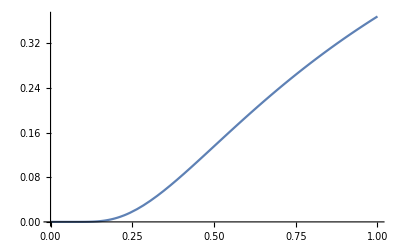

```mathematica
Plot[Exp[-1/x],{x,0,1}]
```

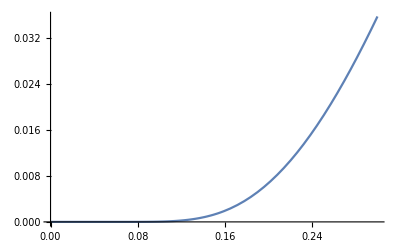

```mathematica
Plot[Exp[-1/x],{x,0,0.3}]
```